```mathematica
Needs["NETLink`"];
Symbol["LoadNETType"]["System.Diagnostics.Process"];
Symbol["LoadNETType"]["System.Diagnostics.ProcessStartInfo"];
Symbol["LoadNETType"]["System.IO.File"];
```

```mathematica
(*Запустить процесс с контролем времени выполнения (в секундах)*)
ExecuteProcess[cmd_, args_,timeout_, output_, error_]:=
Block[{p, f,r,f1, result, killed, memory},
	si = NETNew["System.Diagnostics.ProcessStartInfo", cmd,args];
	si@RedirectStandardOutput = True;
	si@RedirectStandardError = True;
	si@UseShellExecute = False;
	si@CreateNoWindow = True;
	f=File`Create[output];
	f1=File`Create[error];
	p = Process`Start[si];
	p@StandardOutput@BaseStream@CopyToAsync[f];
	p@StandardError@BaseStream@CopyToAsync[f1];
	
	result={};

	killed = False;
	If[0 <timeout < Infinity,
		killed = !p@WaitForExit[Ceiling[ timeout * 1000]];
		If[killed, 
			p@Kill[];
			AppendTo[result, Killed->True];
			AppendTo[result, Timeout->timeout];
		];
	];

	p@WaitForExit[];

	If[!killed,
		AppendTo[result, ExitCode->p@ExitCode]
	];
	
	AppendTo[result, TotalProcessorTime->p@TotalProcessorTime@TotalSeconds];
	AppendTo[result, Time->p@ExitTime@Subtract[ p@StartTime]@TotalSeconds];

	p@StandardOutput@BaseStream@Flush[];
	p@StandardError@BaseStream@Flush[];
	f@Flush[];
	f1@Flush[];
	f@Close[];
	f1@Close[];
	p@Close[];
	Return[result];
];
```

```mathematica
(*Запустить процесс с контролем времени выполнения и получить результат из потоков вывода*)
ExecuteProcessAndOutputLines[cmd_, args_,timeout_]:=
Block[{output = CreateTemporary[],error = CreateTemporary[], result, outputText, errorText},

	If[FileExistsQ[output], 
		DeleteFile[output]];
	If[FileExistsQ[error], 
		DeleteFile[error]];
	
	result = ExecuteProcess[cmd, args, timeout, output, error];

	outputText = Import[output, "Text"];
	errorText = Import[error, "Text"];

	AppendTo[result,OutputText->outputText];
	AppendTo[result,ErrorText->errorText];

	If[FileExistsQ[output], 
		DeleteFile[output]];
	If[FileExistsQ[error], 
		DeleteFile[error]];

	Return[result];
];
```

```mathematica
(*Вызов алгоритма дуализации АО.exe*)
ExecuteLC[dataset_, testds_, config_, log_, timeout_] :=
Block[{result, m, n, count, inner, r, stdout,  extra, avglen, args, meanError},


	args = "--ds " <> dataset <> " --config " <> config;
	If[testds ≠ "", 
		args = args <> " --testds " <> testds;
	];

	If[log ≠ "",
		args = args <> " --log " <> log;
	];

	result = ExecuteProcessAndOutputLines["f:/work/_dual/algorithms_vs2012/release/lc.exe", 
	args, timeout];
	
	stdout = OutputText /. result;

	meanError = StringCases[stdout, "Mean error="~~(x:NumberString):> ToExpression[x]]/.{x_}->x;
	(*m = StringCases[stdout, "m: "~~(x:DigitCharacter..):> ToExpression[x]]/.{x_}->x;
	inner = StringCases[stdout, "inner: "~~(x:DigitCharacter..):> ToExpression[x]]/.{x_}->x;
	extra = StringCases[stdout, "extra: "~~(x:DigitCharacter..):> ToExpression[x]]/.{x_}->x;
	count = StringCases[stdout, "count: "~~(x:DigitCharacter..):> ToExpression[x]]/.{x_}->x;
	avglen = StringCases[stdout, "avgl: "~~(x:NumberString):> ToExpression[x]]/.{x_}->x;*)


	AppendTo[result, "MeanError"->meanError];
	(*AppendTo[result, "m"->m];
	AppendTo[result, "count"->count];
	AppendTo[result, "inner"->inner];
	AppendTo[result, "extra"->extra];
	AppendTo[result, "avglen"->avglen];
	AppendTo[result, "algorithm"->"AO"];
	AppendTo[result, "options"->options];
	AppendTo[result, "inputFile"->FileNameTake[input]];
	AppendTo[result, "inputPath"->input];*)

	result = DeleteCases[result, OutputText->_];
	result = DeleteCases[result, ErrorText->_];
	result = DeleteCases[result, ExitCode->_];

	Return[result];
];
```

```mathematica
Table[
"MeanError" /.
ExecuteLC[
"f:\\work\\_dual\\Algorithms_vs2012\\datasets\\iris.txt", "", conf,
"f:\\work\\_dual\\Algorithms_vs2012\\logs\\lc.log", 600]
,{conf,FileNames["f:\\work\\_dual\\Algorithms_vs2012\\configs\\*.info"]}]
```

FileExistsQ::fstr: File specification output is not a string of one or more characters.

General::stop: Further output of FileExistsQ :: fstr will be suppressed during this calculation.

$Aborted

```mathematica
ExecuteLC[
"f:\\work\\_dual\\Algorithms_vs2012\\test-datasets\\optdigits.int", "", "f:\\work\\_dual\\Algorithms_vs2012\\configs\\ps.info",
"f:\\work\\_dual\\Algorithms_vs2012\\logs\\lc.log", 600]
```

FileExistsQ::fstr: File specification output is not a string of one or more characters.

$Aborted

```mathematica
SetDirectory[NotebookDirectory[]]
```

F:\work\_dual\Algorithms_vs2012\mathematica

```mathematica
StringReplace["..\\experiments\\train-test\\monks-1-train.int" , "-train."-> "-test."]
```

..\experiments\train-test\monks-1-test.int

```mathematica
ExpandFileName["..\\experiments\\train-test\\monks-1-test.int"]
```

F:\work\_dual\Algorithms_vs2012\experiments\train-test\monks-1-test.int

```mathematica
tasks =Flatten[ Table[{dataset,StringReplace[dataset , "-train."-> "-test."], config},
{dataset, FileNames["../experiments/train-test/*-train.int"]},
{config, FileNames["../experiments/train-test/*.info"]}],1];

logs = Table[{"../logs/"<>ToString[i] <>".log"},{i,Range[ Length[tasks]]}];
tasks = Join[tasks, logs,2]
```

{{..\experiments\train-test\letter-recognition-train.int,..\experiments\train-test\letter-recognition-test.int,..\experiments\train-test\boostingec.info,../logs/1.log},{..\experiments\train-test\letter-recognition-train.int,..\experiments\train-test\letter-recognition-test.int,..\experiments\train-test\boostingecmp.info,../logs/2.log},{..\experiments\train-test\letter-recognition-train.int,..\experiments\train-test\letter-recognition-test.int,..\experiments\train-test\boostingecmp-lb.info,../logs/3.log},{..\experiments\train-test\letter-recognition-train.int,..\experiments\train-test\letter-recognition-test.int,..\experiments\train-test\boostingecmp-lb-lazy-bin-boost.info,../logs/4.log},{..\experiments\train-test\letter-recognition-train.int,..\experiments\train-test\letter-recognition-test.int,..\experiments\train-test\boostingecmp-lb-lazy-bin.info,../logs/5.log},{..\experiments\train-test\letter-recognition-train.int,..\experiments\train-test\letter-recognition-test.int,..\experiments\train-test\boostingft.info,../logs/6.log},{..\experiments\train-test\letter-recognition-train.int,..\experiments\train-test\letter-recognition-test.int,..\experiments\train-test\boostingmon.info,../logs/7.log},{..\experiments\train-test\letter-recognition-train.int,..\experiments\train-test\letter-recognition-test.int,..\experiments\train-test\ft.info,../logs/8.log},{..\experiments\train-test\letter-recognition-train.int,..\experiments\train-test\letter-recognition-test.int,..\experiments\train-test\mon.info,../logs/9.log},{..\experiments\train-test\letter-recognition-train.int,..\experiments\train-test\letter-recognition-test.int,..\experiments\train-test\ps.info,../logs/10.log},{..\experiments\train-test\optdigits-train.int,..\experiments\train-test\optdigits-test.int,..\experiments\train-test\boostingec.info,../logs/11.log},{..\experiments\train-test\optdigits-train.int,..\experiments\train-test\optdigits-test.int,..\experiments\train-test\boostingecmp.info,../logs/12.log},{..\experiments\train-test\optdigits-train.int,..\experiments\train-test\optdigits-test.int,..\experiments\train-test\boostingecmp-lb.info,../logs/13.log},{..\experiments\train-test\optdigits-train.int,..\experiments\train-test\optdigits-test.int,..\experiments\train-test\boostingecmp-lb-lazy-bin-boost.info,../logs/14.log},{..\experiments\train-test\optdigits-train.int,..\experiments\train-test\optdigits-test.int,..\experiments\train-test\boostingecmp-lb-lazy-bin.info,../logs/15.log},{..\experiments\train-test\optdigits-train.int,..\experiments\train-test\optdigits-test.int,..\experiments\train-test\boostingft.info,../logs/16.log},{..\experiments\train-test\optdigits-train.int,..\experiments\train-test\optdigits-test.int,..\experiments\train-test\boostingmon.info,../logs/17.log},{..\experiments\train-test\optdigits-train.int,..\experiments\train-test\optdigits-test.int,..\experiments\train-test\ft.info,../logs/18.log},{..\experiments\train-test\optdigits-train.int,..\experiments\train-test\optdigits-test.int,..\experiments\train-test\mon.info,../logs/19.log},{..\experiments\train-test\optdigits-train.int,..\experiments\train-test\optdigits-test.int,..\experiments\train-test\ps.info,../logs/20.log}}

```mathematica
tasks =Flatten[ Table[{dataset, config},
{dataset, FileNames["../experiments/time/*.int"]},
{config, FileNames["../experiments/time/*.info"]}],1];

logs = Table[{"../logs/"<>ToString[i] <>".log"},{i,Range[ Length[tasks]]}];
tasks = Join[tasks, logs,2]
```

{{..\experiments\time\optdigits-1000.int,..\experiments\time\boostingecmp.info,../logs/1.log},{..\experiments\time\optdigits-1000.int,..\experiments\time\boostingecmp-lb.info,../logs/2.log},{..\experiments\time\optdigits-1000.int,..\experiments\time\boostingecmp-lb-lazy-bin-boost.info,../logs/3.log},{..\experiments\time\optdigits-1000.int,..\experiments\time\boostingecmp-lb-lazy-bin.info,../logs/4.log},{..\experiments\time\optdigits-1200.int,..\experiments\time\boostingecmp.info,../logs/5.log},{..\experiments\time\optdigits-1200.int,..\experiments\time\boostingecmp-lb.info,../logs/6.log},{..\experiments\time\optdigits-1200.int,..\experiments\time\boostingecmp-lb-lazy-bin-boost.info,../logs/7.log},{..\experiments\time\optdigits-1200.int,..\experiments\time\boostingecmp-lb-lazy-bin.info,../logs/8.log},{..\experiments\time\optdigits-1400.int,..\experiments\time\boostingecmp.info,../logs/9.log},{..\experiments\time\optdigits-1400.int,..\experiments\time\boostingecmp-lb.info,../logs/10.log},{..\experiments\time\optdigits-1400.int,..\experiments\time\boostingecmp-lb-lazy-bin-boost.info,../logs/11.log},{..\experiments\time\optdigits-1400.int,..\experiments\time\boostingecmp-lb-lazy-bin.info,../logs/12.log},{..\experiments\time\optdigits-1600.int,..\experiments\time\boostingecmp.info,../logs/13.log},{..\experiments\time\optdigits-1600.int,..\experiments\time\boostingecmp-lb.info,../logs/14.log},{..\experiments\time\optdigits-1600.int,..\experiments\time\boostingecmp-lb-lazy-bin-boost.info,../logs/15.log},{..\experiments\time\optdigits-1600.int,..\experiments\time\boostingecmp-lb-lazy-bin.info,../logs/16.log},{..\experiments\time\optdigits-1800.int,..\experiments\time\boostingecmp.info,../logs/17.log},{..\experiments\time\optdigits-1800.int,..\experiments\time\boostingecmp-lb.info,../logs/18.log},{..\experiments\time\optdigits-1800.int,..\experiments\time\boostingecmp-lb-lazy-bin-boost.info,../logs/19.log},{..\experiments\time\optdigits-1800.int,..\experiments\time\boostingecmp-lb-lazy-bin.info,../logs/20.log},{..\experiments\time\optdigits-2000.int,..\experiments\time\boostingecmp.info,../logs/21.log},{..\experiments\time\optdigits-2000.int,..\experiments\time\boostingecmp-lb.info,../logs/22.log},{..\experiments\time\optdigits-2000.int,..\experiments\time\boostingecmp-lb-lazy-bin-boost.info,../logs/23.log},{..\experiments\time\optdigits-2000.int,..\experiments\time\boostingecmp-lb-lazy-bin.info,../logs/24.log},{..\experiments\time\optdigits-200.int,..\experiments\time\boostingecmp.info,../logs/25.log},{..\experiments\time\optdigits-200.int,..\experiments\time\boostingecmp-lb.info,../logs/26.log},{..\experiments\time\optdigits-200.int,..\experiments\time\boostingecmp-lb-lazy-bin-boost.info,../logs/27.log},{..\experiments\time\optdigits-200.int,..\experiments\time\boostingecmp-lb-lazy-bin.info,../logs/28.log},{..\experiments\time\optdigits-400.int,..\experiments\time\boostingecmp.info,../logs/29.log},{..\experiments\time\optdigits-400.int,..\experiments\time\boostingecmp-lb.info,../logs/30.log},{..\experiments\time\optdigits-400.int,..\experiments\time\boostingecmp-lb-lazy-bin-boost.info,../logs/31.log},{..\experiments\time\optdigits-400.int,..\experiments\time\boostingecmp-lb-lazy-bin.info,../logs/32.log},{..\experiments\time\optdigits-600.int,..\experiments\time\boostingecmp.info,../logs/33.log},{..\experiments\time\optdigits-600.int,..\experiments\time\boostingecmp-lb.info,../logs/34.log},{..\experiments\time\optdigits-600.int,..\experiments\time\boostingecmp-lb-lazy-bin-boost.info,../logs/35.log},{..\experiments\time\optdigits-600.int,..\experiments\time\boostingecmp-lb-lazy-bin.info,../logs/36.log},{..\experiments\time\optdigits-800.int,..\experiments\time\boostingecmp.info,../logs/37.log},{..\experiments\time\optdigits-800.int,..\experiments\time\boostingecmp-lb.info,../logs/38.log},{..\experiments\time\optdigits-800.int,..\experiments\time\boostingecmp-lb-lazy-bin-boost.info,../logs/39.log},{..\experiments\time\optdigits-800.int,..\experiments\time\boostingecmp-lb-lazy-bin.info,../logs/40.log}}

```mathematica
Results = {};
CurrentTasks = {};
CompleteTasks = {};
```

```mathematica
DoTask[task_]:=Block[{r}, 
AppendTo[CurrentTasks, task];
 r = ExecuteLC[task[[1]], "",  task[[2]], task[[3]], 3600];
AppendTo[Results, task->r];
Save["results", Results];
CurrentTasks = DeleteCases[CurrentTasks, task];
AppendTo[CompleteTasks, task];
];

DoTask2[task_]:=Block[{r}, 
AppendTo[CurrentTasks, task];
 r = ExecuteLC[task[[1]], task[[2]], task[[3]],task[[4]], 3600];
AppendTo[Results, task->r];
Save["results", Results];
CurrentTasks = DeleteCases[CurrentTasks, task];
AppendTo[CompleteTasks, task];
];
```

```mathematica
Put[TestResults, "results_time_optdigits"];
```

```mathematica
TestResults = Get["results_time_optdigits"]
```

{{..\experiments\time\optdigits-1000.int,..\experiments\time\boostingecmp.info,../logs/1.log}→{TotalProcessorTime→398.411,Time→399.267,MeanError→0},{..\experiments\time\optdigits-1000.int,..\experiments\time\boostingecmp-lb.info,../logs/2.log}→{TotalProcessorTime→573.428,Time→574.395,MeanError→0},{..\experiments\time\optdigits-1000.int,..\experiments\time\boostingecmp-lb-lazy-bin-boost.info,../logs/3.log}→{TotalProcessorTime→134.145,Time→134.288,MeanError→0},{..\experiments\time\optdigits-1000.int,..\experiments\time\boostingecmp-lb-lazy-bin.info,../logs/4.log}→{TotalProcessorTime→145.346,Time→145.548,MeanError→0},{..\experiments\time\optdigits-1200.int,..\experiments\time\boostingecmp.info,../logs/5.log}→{TotalProcessorTime→546.269,Time→546.642,MeanError→0},{..\experiments\time\optdigits-1200.int,..\experiments\time\boostingecmp-lb.info,../logs/6.log}→{TotalProcessorTime→847.475,Time→848.307,MeanError→0},{..\experiments\time\optdigits-1200.int,..\experiments\time\boostingecmp-lb-lazy-bin-boost.info,../logs/7.log}→{TotalProcessorTime→183.488,Time→183.729,MeanError→0},{..\experiments\time\optdigits-1200.int,..\experiments\time\boostingecmp-lb-lazy-bin.info,../logs/8.log}→{TotalProcessorTime→217.871,Time→218.054,MeanError→0},{..\experiments\time\optdigits-1400.int,..\experiments\time\boostingecmp.info,../logs/9.log}→{TotalProcessorTime→641.617,Time→642.615,MeanError→0},{..\experiments\time\optdigits-1400.int,..\experiments\time\boostingecmp-lb.info,../logs/10.log}→{TotalProcessorTime→1254.22,Time→1256.82,MeanError→0},{..\experiments\time\optdigits-1400.int,..\experiments\time\boostingecmp-lb-lazy-bin-boost.info,../logs/11.log}→{TotalProcessorTime→237.917,Time→238.693,MeanError→0},{..\experiments\time\optdigits-1400.int,..\experiments\time\boostingecmp-lb-lazy-bin.info,../logs/12.log}→{TotalProcessorTime→314.872,Time→315.866,MeanError→0},{..\experiments\time\optdigits-1600.int,..\experiments\time\boostingecmp.info,../logs/13.log}→{TotalProcessorTime→818.412,Time→820.389,MeanError→0},{..\experiments\time\optdigits-1600.int,..\experiments\time\boostingecmp-lb.info,../logs/14.log}→{TotalProcessorTime→1538.28,Time→1542.47,MeanError→0},{..\experiments\time\optdigits-1600.int,..\experiments\time\boostingecmp-lb-lazy-bin-boost.info,../logs/15.log}→{TotalProcessorTime→295.949,Time→297.216,MeanError→0},{..\experiments\time\optdigits-1600.int,..\experiments\time\boostingecmp-lb-lazy-bin.info,../logs/16.log}→{TotalProcessorTime→421.702,Time→421.949,MeanError→0},{..\experiments\time\optdigits-1800.int,..\experiments\time\boostingecmp.info,../logs/17.log}→{TotalProcessorTime→984.663,Time→987.218,MeanError→0},{..\experiments\time\optdigits-1800.int,..\experiments\time\boostingecmp-lb.info,../logs/18.log}→{TotalProcessorTime→2005.39,Time→2009.69,MeanError→0},{..\experiments\time\optdigits-1800.int,..\experiments\time\boostingecmp-lb-lazy-bin-boost.info,../logs/19.log}→{TotalProcessorTime→373.966,Time→375.046,MeanError→0},{..\experiments\time\optdigits-1800.int,..\experiments\time\boostingecmp-lb-lazy-bin.info,../logs/20.log}→{TotalProcessorTime→579.169,Time→580.365,MeanError→0},{..\experiments\time\optdigits-2000.int,..\experiments\time\boostingecmp.info,../logs/21.log}→{TotalProcessorTime→1186.08,Time→1188.45,MeanError→0},{..\experiments\time\optdigits-2000.int,..\experiments\time\boostingecmp-lb.info,../logs/22.log}→{TotalProcessorTime→2319.3,Time→2324.06,MeanError→0},{..\experiments\time\optdigits-2000.int,..\experiments\time\boostingecmp-lb-lazy-bin-boost.info,../logs/23.log}→{TotalProcessorTime→482.62,Time→484.501,MeanError→0},{..\experiments\time\optdigits-2000.int,..\experiments\time\boostingecmp-lb-lazy-bin.info,../logs/24.log}→{TotalProcessorTime→710.085,Time→711.444,MeanError→0},{..\experiments\time\optdigits-200.int,..\experiments\time\boostingecmp.info,../logs/25.log}→{TotalProcessorTime→97.173,Time→97.4206,MeanError→0},{..\experiments\time\optdigits-200.int,..\experiments\time\boostingecmp-lb.info,../logs/26.log}→{TotalProcessorTime→39.2811,Time→39.3673,MeanError→0},{..\experiments\time\optdigits-200.int,..\experiments\time\boostingecmp-lb-lazy-bin-boost.info,../logs/27.log}→{TotalProcessorTime→7.73765,Time→7.77544,MeanError→0},{..\experiments\time\optdigits-200.int,..\experiments\time\boostingecmp-lb-lazy-bin.info,../logs/28.log}→{TotalProcessorTime→0.889206,Time→0.909052,MeanError→0},{..\experiments\time\optdigits-400.int,..\experiments\time\boostingecmp.info,../logs/29.log}→{TotalProcessorTime→179.588,Time→181.089,MeanError→0},{..\experiments\time\optdigits-400.int,..\experiments\time\boostingecmp-lb.info,../logs/30.log}→{TotalProcessorTime→128.919,Time→129.749,MeanError→0},{..\experiments\time\optdigits-400.int,..\experiments\time\boostingecmp-lb-lazy-bin-boost.info,../logs/31.log}→{TotalProcessorTime→36.3638,Time→36.4081,MeanError→0},{..\experiments\time\optdigits-400.int,..\experiments\time\boostingecmp-lb-lazy-bin.info,../logs/32.log}→{TotalProcessorTime→8.47085,Time→8.51349,MeanError→0},{..\experiments\time\optdigits-600.int,..\experiments\time\boostingecmp.info,../logs/33.log}→{TotalProcessorTime→241.895,Time→242.93,MeanError→0},{..\experiments\time\optdigits-600.int,..\experiments\time\boostingecmp-lb.info,../logs/34.log}→{TotalProcessorTime→257.043,Time→258.48,MeanError→0},{..\experiments\time\optdigits-600.int,..\experiments\time\boostingecmp-lb-lazy-bin-boost.info,../logs/35.log}→{TotalProcessorTime→70.2473,Time→70.8121,MeanError→0},{..\experiments\time\optdigits-600.int,..\experiments\time\boostingecmp-lb-lazy-bin.info,../logs/36.log}→{TotalProcessorTime→33.0098,Time→33.0419,MeanError→0},{..\experiments\time\optdigits-800.int,..\experiments\time\boostingecmp.info,../logs/37.log}→{TotalProcessorTime→336.494,Time→337.586,MeanError→0},{..\experiments\time\optdigits-800.int,..\experiments\time\boostingecmp-lb.info,../logs/38.log}→{TotalProcessorTime→328.289,Time→328.418,MeanError→0},{..\experiments\time\optdigits-800.int,..\experiments\time\boostingecmp-lb-lazy-bin-boost.info,../logs/39.log}→{TotalProcessorTime→106.923,Time→107.103,MeanError→0},{..\experiments\time\optdigits-800.int,..\experiments\time\boostingecmp-lb-lazy-bin.info,../logs/40.log}→{TotalProcessorTime→89.4198,Time→89.5331,MeanError→0}}

```mathematica
(*Результаты последних 8 экспериментов*)
Dynamic[Results//TableForm]
(*Прогресс выполнения*)
Dynamic[{CurrentTasks //TableForm, Length[tasks], Length[Results]}//TableForm]
```

```mathematica
CloseKernels[];
LaunchKernels[4]
ParallelEvaluate[Needs["NETLink`"];
Symbol["LoadNETType"]["System.Diagnostics.Process"];
Symbol["LoadNETType"]["System.Diagnostics.ProcessStartInfo"];
Symbol["LoadNETType"]["System.IO.File"];];

SetSharedVariable[tasks,CurrentTasks, CompleteTasks, Results]
DistributeDefinitions[DoTask, DoTask2]
```

{KernelObject[27,local],KernelObject[28,local],KernelObject[29,local],KernelObject[30,local]}

{DoTask,DoTask2}

```mathematica
Parallelize[Scan[DoTask, tasks],Method->"FinestGrained"]
```

```mathematica
Partition[TestResults,8]//TableForm
```

{..\experiments\loo\ex10.int,..\experiments\loo\boostingec.info,../logs/1.log}→{TotalProcessorTime→0.0156001,Time→0.0610122,MeanError→0.4} | {..\experiments\loo\ex10.int,..\experiments\loo\boostingecmp.info,../logs/2.log}→{TotalProcessorTime→0.0312002,Time→0.0770154,MeanError→0.2} | {..\experiments\loo\ex10.int,..\experiments\loo\boostingecmp-lb.info,../logs/3.log}→{TotalProcessorTime→0.0156001,Time→0.0690138,MeanError→0.1} | {..\experiments\loo\ex10.int,..\experiments\loo\boostingft.info,../logs/4.log}→{TotalProcessorTime→0.0156001,Time→0.040008,MeanError→0.7} | {..\experiments\loo\ex10.int,..\experiments\loo\boostingmon.info,../logs/5.log}→{TotalProcessorTime→0.0156001,Time→0.0540108,MeanError→0.5} | {..\experiments\loo\ex10.int,..\experiments\loo\ft.info,../logs/6.log}→{TotalProcessorTime→0.,Time→0.0580116,MeanError→1} | {..\experiments\loo\ex10.int,..\experiments\loo\mon.info,../logs/7.log}→{TotalProcessorTime→0.0156001,Time→0.0310062,MeanError→0.4} | {..\experiments\loo\ex10.int,..\experiments\loo\ps.info,../logs/8.log}→{TotalProcessorTime→0.,Time→0.0430086,MeanError→0.5}
{..\experiments\loo\ex11.int,..\experiments\loo\boostingec.info,../logs/9.log}→{TotalProcessorTime→0.0156001,Time→0.0580116,MeanError→0.5} | {..\experiments\loo\ex11.int,..\experiments\loo\boostingecmp.info,../logs/10.log}→{TotalProcessorTime→0.0156001,Time→0.045009,MeanError→0.333333} | {..\experiments\loo\ex11.int,..\experiments\loo\boostingecmp-lb.info,../logs/11.log}→{TotalProcessorTime→0.0156001,Time→0.0580116,MeanError→0.333333} | {..\experiments\loo\ex11.int,..\experiments\loo\boostingft.info,../logs/12.log}→{TotalProcessorTime→0.0156001,Time→0.0510102,MeanError→0.833333} | {..\experiments\loo\ex11.int,..\experiments\loo\boostingmon.info,../logs/13.log}→{TotalProcessorTime→0.0156001,Time→0.040008,MeanError→0.416667} | {..\experiments\loo\ex11.int,..\experiments\loo\ft.info,../logs/14.log}→{TotalProcessorTime→0.0156001,Time→0.0390078,MeanError→1} | {..\experiments\loo\ex11.int,..\experiments\loo\mon.info,../logs/15.log}→{TotalProcessorTime→0.0156001,Time→0.0490098,MeanError→0.666667} | {..\experiments\loo\ex11.int,..\experiments\loo\ps.info,../logs/16.log}→{TotalProcessorTime→0.0312002,Time→0.0310062,MeanError→0.5}
{..\experiments\loo\ex12.int,..\experiments\loo\boostingec.info,../logs/17.log}→{TotalProcessorTime→0.0156001,Time→0.0490098,MeanError→0.428571} | {..\experiments\loo\ex12.int,..\experiments\loo\boostingecmp.info,../logs/18.log}→{TotalProcessorTime→0.0312002,Time→0.0660132,MeanError→0.357143} | {..\experiments\loo\ex12.int,..\experiments\loo\boostingecmp-lb.info,../logs/19.log}→{TotalProcessorTime→0.0312002,Time→0.0580116,MeanError→0.428571} | {..\experiments\loo\ex12.int,..\experiments\loo\boostingft.info,../logs/20.log}→{TotalProcessorTime→0.0156001,Time→0.0420084,MeanError→0.714286} | {..\experiments\loo\ex12.int,..\experiments\loo\boostingmon.info,../logs/21.log}→{TotalProcessorTime→0.0156001,Time→0.0440088,MeanError→0.5} | {..\experiments\loo\ex12.int,..\experiments\loo\ft.info,../logs/22.log}→{TotalProcessorTime→0.,Time→0.0330066,MeanError→0.857143} | {..\experiments\loo\ex12.int,..\experiments\loo\mon.info,../logs/23.log}→{TotalProcessorTime→0.,Time→0.0360072,MeanError→0.5} | {..\experiments\loo\ex12.int,..\experiments\loo\ps.info,../logs/24.log}→{TotalProcessorTime→0.0312002,Time→0.0330066,MeanError→0.428571}
{..\experiments\loo\ex13.int,..\experiments\loo\boostingec.info,../logs/25.log}→{TotalProcessorTime→0.,Time→0.040008,MeanError→0.2} | {..\experiments\loo\ex13.int,..\experiments\loo\boostingecmp.info,../logs/26.log}→{TotalProcessorTime→0.0156001,Time→0.05001,MeanError→0.133333} | {..\experiments\loo\ex13.int,..\experiments\loo\boostingecmp-lb.info,../logs/27.log}→{TotalProcessorTime→0.0312002,Time→0.0530106,MeanError→0.133333} | {..\experiments\loo\ex13.int,..\experiments\loo\boostingft.info,../logs/28.log}→{TotalProcessorTime→0.0156001,Time→0.040008,MeanError→0.666667} | {..\experiments\loo\ex13.int,..\experiments\loo\boostingmon.info,../logs/29.log}→{TotalProcessorTime→0.0156001,Time→0.0430086,MeanError→0.133333} | {..\experiments\loo\ex13.int,..\experiments\loo\ft.info,../logs/30.log}→{TotalProcessorTime→0.,Time→0.0390078,MeanError→0.733333} | {..\experiments\loo\ex13.int,..\experiments\loo\mon.info,../logs/31.log}→{TotalProcessorTime→0.0156001,Time→0.0310062,MeanError→0.2} | {..\experiments\loo\ex13.int,..\experiments\loo\ps.info,../logs/32.log}→{TotalProcessorTime→0.,Time→0.0320064,MeanError→0.2}
{..\experiments\loo\ex14.int,..\experiments\loo\boostingec.info,../logs/33.log}→{TotalProcessorTime→0.0156001,Time→0.0360072,MeanError→0.4} | {..\experiments\loo\ex14.int,..\experiments\loo\boostingecmp.info,../logs/34.log}→{TotalProcessorTime→0.0156001,Time→0.0340068,MeanError→0.6} | {..\experiments\loo\ex14.int,..\experiments\loo\boostingecmp-lb.info,../logs/35.log}→{TotalProcessorTime→0.0156001,Time→0.040008,MeanError→0.6} | {..\experiments\loo\ex14.int,..\experiments\loo\boostingft.info,../logs/36.log}→{TotalProcessorTime→0.,Time→0.0310062,MeanError→0.6} | {..\experiments\loo\ex14.int,..\experiments\loo\boostingmon.info,../logs/37.log}→{TotalProcessorTime→0.0156001,Time→0.0330066,MeanError→0.6} | {..\experiments\loo\ex14.int,..\experiments\loo\ft.info,../logs/38.log}→{TotalProcessorTime→0.0156001,Time→0.035007,MeanError→0.6} | {..\experiments\loo\ex14.int,..\experiments\loo\mon.info,../logs/39.log}→{TotalProcessorTime→0.,Time→0.035007,MeanError→0.6} | {..\experiments\loo\ex14.int,..\experiments\loo\ps.info,../logs/40.log}→{TotalProcessorTime→0.,Time→0.030006,MeanError→0.6}
{..\experiments\loo\ex15.int,..\experiments\loo\boostingec.info,../logs/41.log}→{TotalProcessorTime→0.0156001,Time→0.0420084,MeanError→0.875} | {..\experiments\loo\ex15.int,..\experiments\loo\boostingecmp.info,../logs/42.log}→{TotalProcessorTime→0.0156001,Time→0.0390078,MeanError→0.875} | {..\experiments\loo\ex15.int,..\experiments\loo\boostingecmp-lb.info,../logs/43.log}→{TotalProcessorTime→0.0312002,Time→0.0510102,MeanError→1} | {..\experiments\loo\ex15.int,..\experiments\loo\boostingft.info,../logs/44.log}→{TotalProcessorTime→0.,Time→0.0490098,MeanError→1} | {..\experiments\loo\ex15.int,..\experiments\loo\boostingmon.info,../logs/45.log}→{TotalProcessorTime→0.0156001,Time→0.0380076,MeanError→0.75} | {..\experiments\loo\ex15.int,..\experiments\loo\ft.info,../logs/46.log}→{TotalProcessorTime→0.,Time→0.075015,MeanError→1} | {..\experiments\loo\ex15.int,..\experiments\loo\mon.info,../logs/47.log}→{TotalProcessorTime→0.0156001,Time→0.0540108,MeanError→0.75} | {..\experiments\loo\ex15.int,..\experiments\loo\ps.info,../logs/48.log}→{TotalProcessorTime→0.0156001,Time→0.065013,MeanError→1}
{..\experiments\loo\ex16.int,..\experiments\loo\boostingec.info,../logs/49.log}→{TotalProcessorTime→0.0156001,Time→0.0710142,MeanError→0.35} | {..\experiments\loo\ex16.int,..\experiments\loo\boostingecmp.info,../logs/50.log}→{TotalProcessorTime→0.0468003,Time→0.0940188,MeanError→0.2} | {..\experiments\loo\ex16.int,..\experiments\loo\boostingecmp-lb.info,../logs/51.log}→{TotalProcessorTime→0.0312002,Time→0.0940188,MeanError→0.4} | {..\experiments\loo\ex16.int,..\experiments\loo\boostingft.info,../logs/52.log}→{TotalProcessorTime→0.0312002,Time→0.0660132,MeanError→0.5} | {..\experiments\loo\ex16.int,..\experiments\loo\boostingmon.info,../logs/53.log}→{TotalProcessorTime→0.,Time→0.0840168,MeanError→0.4} | {..\experiments\loo\ex16.int,..\experiments\loo\ft.info,../logs/54.log}→{TotalProcessorTime→0.,Time→0.0580116,MeanError→1} | {..\experiments\loo\ex16.int,..\experiments\loo\mon.info,../logs/55.log}→{TotalProcessorTime→0.,Time→0.0520104,MeanError→0.35} | {..\experiments\loo\ex16.int,..\experiments\loo\ps.info,../logs/56.log}→{TotalProcessorTime→0.,Time→0.0610122,MeanError→0.4}
{..\experiments\loo\ex1.int,..\experiments\loo\boostingec.info,../logs/57.log}→{TotalProcessorTime→0.0156001,Time→0.0730146,MeanError→0.111111} | {..\experiments\loo\ex1.int,..\experiments\loo\boostingecmp.info,../logs/58.log}→{TotalProcessorTime→0.0156001,Time→0.0410082,MeanError→0.333333} | {..\experiments\loo\ex1.int,..\experiments\loo\boostingecmp-lb.info,../logs/59.log}→{TotalProcessorTime→0.,Time→0.0520104,MeanError→0.111111} | {..\experiments\loo\ex1.int,..\experiments\loo\boostingft.info,../logs/60.log}→{TotalProcessorTime→0.0156001,Time→0.0370074,MeanError→0.666667} | {..\experiments\loo\ex1.int,..\experiments\loo\boostingmon.info,../logs/61.log}→{TotalProcessorTime→0.0156001,Time→0.060012,MeanError→0.111111} | {..\experiments\loo\ex1.int,..\experiments\loo\ft.info,../logs/62.log}→{TotalProcessorTime→0.,Time→0.0770154,MeanError→1} | {..\experiments\loo\ex1.int,..\experiments\loo\mon.info,../logs/63.log}→{TotalProcessorTime→0.0312002,Time→0.0770154,MeanError→0.444444} | {..\experiments\loo\ex1.int,..\experiments\loo\ps.info,../logs/64.log}→{TotalProcessorTime→0.0312002,Time→0.060012,MeanError→0.222222}
{..\experiments\loo\ex2.int,..\experiments\loo\boostingec.info,../logs/65.log}→{TotalProcessorTime→0.0156001,Time→0.0610122,MeanError→0.333333} | {..\experiments\loo\ex2.int,..\experiments\loo\boostingecmp.info,../logs/66.log}→{TotalProcessorTime→0.0312002,Time→0.103021,MeanError→0.277778} | {..\experiments\loo\ex2.int,..\experiments\loo\boostingecmp-lb.info,../logs/67.log}→{TotalProcessorTime→0.0468003,Time→0.0670134,MeanError→0.277778} | {..\experiments\loo\ex2.int,..\experiments\loo\boostingft.info,../logs/68.log}→{TotalProcessorTime→0.0156001,Time→0.0570114,MeanError→0.5} | {..\experiments\loo\ex2.int,..\experiments\loo\boostingmon.info,../logs/69.log}→{TotalProcessorTime→0.0156001,Time→0.045009,MeanError→0.333333} | {..\experiments\loo\ex2.int,..\experiments\loo\ft.info,../logs/70.log}→{TotalProcessorTime→0.,Time→0.0410082,MeanError→1} | {..\experiments\loo\ex2.int,..\experiments\loo\mon.info,../logs/71.log}→{TotalProcessorTime→0.0156001,Time→0.0530106,MeanError→0.555556} | {..\experiments\loo\ex2.int,..\experiments\loo\ps.info,../logs/72.log}→{TotalProcessorTime→0.,Time→0.0340068,MeanError→0.333333}
{..\experiments\loo\ex3.int,..\experiments\loo\boostingec.info,../logs/73.log}→{TotalProcessorTime→0.0156001,Time→0.0360072,MeanError→0.25} | {..\experiments\loo\ex3.int,..\experiments\loo\boostingecmp.info,../logs/74.log}→{TotalProcessorTime→0.0312002,Time→0.0560112,MeanError→0} | {..\experiments\loo\ex3.int,..\experiments\loo\boostingecmp-lb.info,../logs/75.log}→{TotalProcessorTime→0.0468003,Time→0.0720144,MeanError→0.25} | {..\experiments\loo\ex3.int,..\experiments\loo\boostingft.info,../logs/76.log}→{TotalProcessorTime→0.0156001,Time→0.0440088,MeanError→0.9375} | {..\experiments\loo\ex3.int,..\experiments\loo\boostingmon.info,../logs/77.log}→{TotalProcessorTime→0.0156001,Time→0.0670134,MeanError→0.25} | {..\experiments\loo\ex3.int,..\experiments\loo\ft.info,../logs/78.log}→{TotalProcessorTime→0.,Time→0.0640128,MeanError→1} | {..\experiments\loo\ex3.int,..\experiments\loo\mon.info,../logs/79.log}→{TotalProcessorTime→0.,Time→0.0670134,MeanError→0.3125} | {..\experiments\loo\ex3.int,..\experiments\loo\ps.info,../logs/80.log}→{TotalProcessorTime→0.0156001,Time→0.0570114,MeanError→0.25}
{..\experiments\loo\ex4.int,..\experiments\loo\boostingec.info,../logs/81.log}→{TotalProcessorTime→0.,Time→0.0670134,MeanError→0.5} | {..\experiments\loo\ex4.int,..\experiments\loo\boostingecmp.info,../logs/82.log}→{TotalProcessorTime→0.0156001,Time→0.080016,MeanError→0.5} | {..\experiments\loo\ex4.int,..\experiments\loo\boostingecmp-lb.info,../logs/83.log}→{TotalProcessorTime→0.0156001,Time→0.0460092,MeanError→0} | {..\experiments\loo\ex4.int,..\experiments\loo\boostingft.info,../logs/84.log}→{TotalProcessorTime→0.,Time→0.0580116,MeanError→0.5} | {..\experiments\loo\ex4.int,..\experiments\loo\boostingmon.info,../logs/85.log}→{TotalProcessorTime→0.,Time→0.045009,MeanError→0.5} | {..\experiments\loo\ex4.int,..\experiments\loo\ft.info,../logs/86.log}→{TotalProcessorTime→0.0156001,Time→0.030006,MeanError→0.5} | {..\experiments\loo\ex4.int,..\experiments\loo\mon.info,../logs/87.log}→{TotalProcessorTime→0.,Time→0.040008,MeanError→0.5} | {..\experiments\loo\ex4.int,..\experiments\loo\ps.info,../logs/88.log}→{TotalProcessorTime→0.,Time→0.0490098,MeanError→0.5}
{..\experiments\loo\ex5.int,..\experiments\loo\boostingec.info,../logs/89.log}→{TotalProcessorTime→0.0156001,Time→0.0420084,MeanError→0.5} | {..\experiments\loo\ex5.int,..\experiments\loo\boostingecmp.info,../logs/90.log}→{TotalProcessorTime→0.0312002,Time→0.055011,MeanError→0.5} | {..\experiments\loo\ex5.int,..\experiments\loo\boostingecmp-lb.info,../logs/91.log}→{TotalProcessorTime→0.0156001,Time→0.0590118,MeanError→0} | {..\experiments\loo\ex5.int,..\experiments\loo\boostingft.info,../logs/92.log}→{TotalProcessorTime→0.0156001,Time→0.0680136,MeanError→0.916667} | {..\experiments\loo\ex5.int,..\experiments\loo\boostingmon.info,../logs/93.log}→{TotalProcessorTime→0.,Time→0.0580116,MeanError→0.5} | {..\experiments\loo\ex5.int,..\experiments\loo\ft.info,../logs/94.log}→{TotalProcessorTime→0.,Time→0.0710142,MeanError→1} | {..\experiments\loo\ex5.int,..\experiments\loo\mon.info,../logs/95.log}→{TotalProcessorTime→0.0156001,Time→0.0610122,MeanError→0.5} | {..\experiments\loo\ex5.int,..\experiments\loo\ps.info,../logs/96.log}→{TotalProcessorTime→0.,Time→0.0480096,MeanError→0.5}
{..\experiments\loo\ex6.int,..\experiments\loo\boostingec.info,../logs/97.log}→{TotalProcessorTime→0.0156001,Time→0.0710142,MeanError→0.333333} | {..\experiments\loo\ex6.int,..\experiments\loo\boostingecmp.info,../logs/98.log}→{TotalProcessorTime→0.0156001,Time→0.0560112,MeanError→0.333333} | {..\experiments\loo\ex6.int,..\experiments\loo\boostingecmp-lb.info,../logs/99.log}→{TotalProcessorTime→0.0156001,Time→0.0730146,MeanError→0.333333} | {..\experiments\loo\ex6.int,..\experiments\loo\boostingft.info,../logs/100.log}→{TotalProcessorTime→0.0156001,Time→0.0580116,MeanError→0.583333} | {..\experiments\loo\ex6.int,..\experiments\loo\boostingmon.info,../logs/101.log}→{TotalProcessorTime→0.0156001,Time→0.0690138,MeanError→0.333333} | {..\experiments\loo\ex6.int,..\experiments\loo\ft.info,../logs/102.log}→{TotalProcessorTime→0.0156001,Time→0.0530106,MeanError→1} | {..\experiments\loo\ex6.int,..\experiments\loo\mon.info,../logs/103.log}→{TotalProcessorTime→0.0156001,Time→0.075015,MeanError→0.166667} | {..\experiments\loo\ex6.int,..\experiments\loo\ps.info,../logs/104.log}→{TotalProcessorTime→0.,Time→0.0390078,MeanError→0.333333}
{..\experiments\loo\ex7.int,..\experiments\loo\boostingec.info,../logs/105.log}→{TotalProcessorTime→0.0156001,Time→0.0460092,MeanError→0.2} | {..\experiments\loo\ex7.int,..\experiments\loo\boostingecmp.info,../logs/106.log}→{TotalProcessorTime→0.0156001,Time→0.045009,MeanError→0.2} | {..\experiments\loo\ex7.int,..\experiments\loo\boostingecmp-lb.info,../logs/107.log}→{TotalProcessorTime→0.0312002,Time→0.0570114,MeanError→0.2} | {..\experiments\loo\ex7.int,..\experiments\loo\boostingft.info,../logs/108.log}→{TotalProcessorTime→0.,Time→0.0620124,MeanError→0.4} | {..\experiments\loo\ex7.int,..\experiments\loo\boostingmon.info,../logs/109.log}→{TotalProcessorTime→0.0156001,Time→0.0640128,MeanError→0.2} | {..\experiments\loo\ex7.int,..\experiments\loo\ft.info,../logs/110.log}→{TotalProcessorTime→0.,Time→0.0520104,MeanError→1} | {..\experiments\loo\ex7.int,..\experiments\loo\mon.info,../logs/111.log}→{TotalProcessorTime→0.0156001,Time→0.055011,MeanError→0.2} | {..\experiments\loo\ex7.int,..\experiments\loo\ps.info,../logs/112.log}→{TotalProcessorTime→0.,Time→0.0610122,MeanError→0.2}
{..\experiments\loo\ex8.int,..\experiments\loo\boostingec.info,../logs/113.log}→{TotalProcessorTime→0.0156001,Time→0.0580116,MeanError→0.833333} | {..\experiments\loo\ex8.int,..\experiments\loo\boostingecmp.info,../logs/114.log}→{TotalProcessorTime→0.0312002,Time→0.0820164,MeanError→0.0833333} | {..\experiments\loo\ex8.int,..\experiments\loo\boostingecmp-lb.info,../logs/115.log}→{TotalProcessorTime→0.0156001,Time→0.0720144,MeanError→0.416667} | {..\experiments\loo\ex8.int,..\experiments\loo\boostingft.info,../logs/116.log}→{TotalProcessorTime→0.0156001,Time→0.0330066,MeanError→1} | {..\experiments\loo\ex8.int,..\experiments\loo\boostingmon.info,../logs/117.log}→{TotalProcessorTime→0.0156001,Time→0.0620124,MeanError→0.5} | {..\experiments\loo\ex8.int,..\experiments\loo\ft.info,../logs/118.log}→{TotalProcessorTime→0.,Time→0.0440088,MeanError→1} | {..\experiments\loo\ex8.int,..\experiments\loo\mon.info,../logs/119.log}→{TotalProcessorTime→0.,Time→0.0730146,MeanError→0.5} | {..\experiments\loo\ex8.int,..\experiments\loo\ps.info,../logs/120.log}→{TotalProcessorTime→0.0156001,Time→0.065013,MeanError→0.583333}
{..\experiments\loo\ex9.int,..\experiments\loo\boostingec.info,../logs/121.log}→{TotalProcessorTime→0.,Time→0.0590118,MeanError→0.5} | {..\experiments\loo\ex9.int,..\experiments\loo\boostingecmp.info,../logs/122.log}→{TotalProcessorTime→0.0624004,Time→0.0930186,MeanError→0.4375} | {..\experiments\loo\ex9.int,..\experiments\loo\boostingecmp-lb.info,../logs/123.log}→{TotalProcessorTime→0.0312002,Time→0.075015,MeanError→0.4375} | {..\experiments\loo\ex9.int,..\experiments\loo\boostingft.info,../logs/124.log}→{TotalProcessorTime→0.0156001,Time→0.0730146,MeanError→0.875} | {..\experiments\loo\ex9.int,..\experiments\loo\boostingmon.info,../logs/125.log}→{TotalProcessorTime→0.0156001,Time→0.065013,MeanError→0.5625} | {..\experiments\loo\ex9.int,..\experiments\loo\ft.info,../logs/126.log}→{TotalProcessorTime→0.,Time→0.060012,MeanError→1} | {..\experiments\loo\ex9.int,..\experiments\loo\mon.info,../logs/127.log}→{TotalProcessorTime→0.0312002,Time→0.0740148,MeanError→0.5} | {..\experiments\loo\ex9.int,..\experiments\loo\ps.info,../logs/128.log}→{TotalProcessorTime→0.,Time→0.0570114,MeanError→0.5}
{..\experiments\loo\lenses.int,..\experiments\loo\boostingec.info,../logs/129.log}→{TotalProcessorTime→0.0312002,Time→0.0960192,MeanError→0.333333} | {..\experiments\loo\lenses.int,..\experiments\loo\boostingecmp.info,../logs/130.log}→{TotalProcessorTime→0.0624004,Time→0.123025,MeanError→0.25} | {..\experiments\loo\lenses.int,..\experiments\loo\boostingecmp-lb.info,../logs/131.log}→{TotalProcessorTime→0.0936006,Time→0.118024,MeanError→0.291667} | {..\experiments\loo\lenses.int,..\experiments\loo\boostingft.info,../logs/132.log}→{TotalProcessorTime→0.0156001,Time→0.0530106,MeanError→0.25} | {..\experiments\loo\lenses.int,..\experiments\loo\boostingmon.info,../logs/133.log}→{TotalProcessorTime→0.0312002,Time→0.060012,MeanError→0.25} | {..\experiments\loo\lenses.int,..\experiments\loo\ft.info,../logs/134.log}→{TotalProcessorTime→0.,Time→0.0480096,MeanError→1} | {..\experiments\loo\lenses.int,..\experiments\loo\mon.info,../logs/135.log}→{TotalProcessorTime→0.0156001,Time→0.0490098,MeanError→0.291667} | {..\experiments\loo\lenses.int,..\experiments\loo\ps.info,../logs/136.log}→{TotalProcessorTime→0.,Time→0.0620124,MeanError→0.208333}
{..\experiments\loo\soybean-small.int,..\experiments\loo\boostingec.info,../logs/137.log}→{TotalProcessorTime→0.109201,Time→0.175035,MeanError→0} | {..\experiments\loo\soybean-small.int,..\experiments\loo\boostingecmp.info,../logs/138.log}→{TotalProcessorTime→1.77841,Time→1.82336,MeanError→0} | {..\experiments\loo\soybean-small.int,..\experiments\loo\boostingecmp-lb.info,../logs/139.log}→{TotalProcessorTime→0.187201,Time→0.189038,MeanError→0.0425532} | {..\experiments\loo\soybean-small.int,..\experiments\loo\boostingft.info,../logs/140.log}→{TotalProcessorTime→0.265202,Time→0.307061,MeanError→0.0212766} | {..\experiments\loo\soybean-small.int,..\experiments\loo\boostingmon.info,../logs/141.log}→{TotalProcessorTime→0.452403,Time→0.479096,MeanError→0} | {..\experiments\loo\soybean-small.int,..\experiments\loo\ft.info,../logs/142.log}→{TotalProcessorTime→0.421203,Time→0.473095,MeanError→0.0212766} | {..\experiments\loo\soybean-small.int,..\experiments\loo\mon.info,../logs/143.log}→{TotalProcessorTime→0.421203,Time→0.456091,MeanError→0} | {..\experiments\loo\soybean-small.int,..\experiments\loo\ps.info,../logs/144.log}→{TotalProcessorTime→0.109201,Time→0.121024,MeanError→0.0212766}
{..\experiments\loo\xor.int,..\experiments\loo\boostingec.info,../logs/145.log}→{TotalProcessorTime→0.0312002,Time→0.040008,MeanError→1} | {..\experiments\loo\xor.int,..\experiments\loo\boostingecmp.info,../logs/146.log}→{TotalProcessorTime→0.,Time→0.035007,MeanError→1} | {..\experiments\loo\xor.int,..\experiments\loo\boostingecmp-lb.info,../logs/147.log}→{TotalProcessorTime→0.0156001,Time→0.0370074,MeanError→1} | {..\experiments\loo\xor.int,..\experiments\loo\boostingft.info,../logs/148.log}→{TotalProcessorTime→0.,Time→0.0330066,MeanError→1} | {..\experiments\loo\xor.int,..\experiments\loo\boostingmon.info,../logs/149.log}→{TotalProcessorTime→0.,Time→0.0370074,MeanError→1} | {..\experiments\loo\xor.int,..\experiments\loo\ft.info,../logs/150.log}→{TotalProcessorTime→0.,Time→0.040008,MeanError→1} | {..\experiments\loo\xor.int,..\experiments\loo\mon.info,../logs/151.log}→{TotalProcessorTime→0.,Time→0.0290058,MeanError→1} | {..\experiments\loo\xor.int,..\experiments\loo\ps.info,../logs/152.log}→{TotalProcessorTime→0.,Time→0.0310062,MeanError→1}

```mathematica
data = Partition[TestResults,10] [[;;,{8,10,9,6,1,7,2,3,5,4}]];
TableForm[ ("MeanError" /. data[[;;,;;,2]])/.{}->"???",
TableHeadings->{
Map[FileBaseName,data[[;;,1,1,1]]], 
Rotate[#,80 Degree]&/@FileBaseName /@ data[[1,;;,1,3]]
}]
```

| ft | ps | mon | boostingft | boostingec | boostingmon | boostingecmp | boostingecmp-lb | boostingecmp-lb-lazy-bin | boostingecmp-lb-lazy-bin-boost
letter-recognition-train | 0.517629 | 0.208528 | 0.632241 | 0.214561 | 0.165679 | 0.24961 | ??? | ??? | 0.234217 | 0.254082
optdigits-train | 0.769616 | 0.190874 | 0.547579 | 0.25153 | 0.228158 | 0.167501 | 0.151363 | ??? | 0.272677 | 0.143016

```mathematica
TableForm[ Partition[TestResults[[;;,2,-1,2]],10] ,
TableHeadings->{
Map[FileNameTake,Partition[TestResults,10][[;;,1,1,1]]], 
Rotate[#,60 Degree]&/@FileNameTake /@ Partition[TestResults,10][[1,;;,1,3]]
}]
```

```mathematica
TestResults = SortBy[ Results, #[[1,1;;2]]&]
```

{{..\experiments\time\optdigits-1000.int,..\experiments\time\boostingecmp.info,../logs/1.log}→{TotalProcessorTime→398.411,Time→399.267,MeanError→0},{..\experiments\time\optdigits-1000.int,..\experiments\time\boostingecmp-lb.info,../logs/2.log}→{TotalProcessorTime→573.428,Time→574.395,MeanError→0},{..\experiments\time\optdigits-1000.int,..\experiments\time\boostingecmp-lb-lazy-bin-boost.info,../logs/3.log}→{TotalProcessorTime→134.145,Time→134.288,MeanError→0},{..\experiments\time\optdigits-1000.int,..\experiments\time\boostingecmp-lb-lazy-bin.info,../logs/4.log}→{TotalProcessorTime→145.346,Time→145.548,MeanError→0},{..\experiments\time\optdigits-1200.int,..\experiments\time\boostingecmp.info,../logs/5.log}→{TotalProcessorTime→546.269,Time→546.642,MeanError→0},{..\experiments\time\optdigits-1200.int,..\experiments\time\boostingecmp-lb.info,../logs/6.log}→{TotalProcessorTime→847.475,Time→848.307,MeanError→0},{..\experiments\time\optdigits-1200.int,..\experiments\time\boostingecmp-lb-lazy-bin-boost.info,../logs/7.log}→{TotalProcessorTime→183.488,Time→183.729,MeanError→0},{..\experiments\time\optdigits-1200.int,..\experiments\time\boostingecmp-lb-lazy-bin.info,../logs/8.log}→{TotalProcessorTime→217.871,Time→218.054,MeanError→0},{..\experiments\time\optdigits-1400.int,..\experiments\time\boostingecmp.info,../logs/9.log}→{TotalProcessorTime→641.617,Time→642.615,MeanError→0},{..\experiments\time\optdigits-1400.int,..\experiments\time\boostingecmp-lb.info,../logs/10.log}→{TotalProcessorTime→1254.22,Time→1256.82,MeanError→0},{..\experiments\time\optdigits-1400.int,..\experiments\time\boostingecmp-lb-lazy-bin-boost.info,../logs/11.log}→{TotalProcessorTime→237.917,Time→238.693,MeanError→0},{..\experiments\time\optdigits-1400.int,..\experiments\time\boostingecmp-lb-lazy-bin.info,../logs/12.log}→{TotalProcessorTime→314.872,Time→315.866,MeanError→0},{..\experiments\time\optdigits-1600.int,..\experiments\time\boostingecmp.info,../logs/13.log}→{TotalProcessorTime→818.412,Time→820.389,MeanError→0},{..\experiments\time\optdigits-1600.int,..\experiments\time\boostingecmp-lb.info,../logs/14.log}→{TotalProcessorTime→1538.28,Time→1542.47,MeanError→0},{..\experiments\time\optdigits-1600.int,..\experiments\time\boostingecmp-lb-lazy-bin-boost.info,../logs/15.log}→{TotalProcessorTime→295.949,Time→297.216,MeanError→0},{..\experiments\time\optdigits-1600.int,..\experiments\time\boostingecmp-lb-lazy-bin.info,../logs/16.log}→{TotalProcessorTime→421.702,Time→421.949,MeanError→0},{..\experiments\time\optdigits-1800.int,..\experiments\time\boostingecmp.info,../logs/17.log}→{TotalProcessorTime→984.663,Time→987.218,MeanError→0},{..\experiments\time\optdigits-1800.int,..\experiments\time\boostingecmp-lb.info,../logs/18.log}→{TotalProcessorTime→2005.39,Time→2009.69,MeanError→0},{..\experiments\time\optdigits-1800.int,..\experiments\time\boostingecmp-lb-lazy-bin-boost.info,../logs/19.log}→{TotalProcessorTime→373.966,Time→375.046,MeanError→0},{..\experiments\time\optdigits-1800.int,..\experiments\time\boostingecmp-lb-lazy-bin.info,../logs/20.log}→{TotalProcessorTime→579.169,Time→580.365,MeanError→0},{..\experiments\time\optdigits-2000.int,..\experiments\time\boostingecmp.info,../logs/21.log}→{TotalProcessorTime→1186.08,Time→1188.45,MeanError→0},{..\experiments\time\optdigits-2000.int,..\experiments\time\boostingecmp-lb.info,../logs/22.log}→{TotalProcessorTime→2319.3,Time→2324.06,MeanError→0},{..\experiments\time\optdigits-2000.int,..\experiments\time\boostingecmp-lb-lazy-bin-boost.info,../logs/23.log}→{TotalProcessorTime→482.62,Time→484.501,MeanError→0},{..\experiments\time\optdigits-2000.int,..\experiments\time\boostingecmp-lb-lazy-bin.info,../logs/24.log}→{TotalProcessorTime→710.085,Time→711.444,MeanError→0},{..\experiments\time\optdigits-200.int,..\experiments\time\boostingecmp.info,../logs/25.log}→{TotalProcessorTime→97.173,Time→97.4206,MeanError→0},{..\experiments\time\optdigits-200.int,..\experiments\time\boostingecmp-lb.info,../logs/26.log}→{TotalProcessorTime→39.2811,Time→39.3673,MeanError→0},{..\experiments\time\optdigits-200.int,..\experiments\time\boostingecmp-lb-lazy-bin-boost.info,../logs/27.log}→{TotalProcessorTime→7.73765,Time→7.77544,MeanError→0},{..\experiments\time\optdigits-200.int,..\experiments\time\boostingecmp-lb-lazy-bin.info,../logs/28.log}→{TotalProcessorTime→0.889206,Time→0.909052,MeanError→0},{..\experiments\time\optdigits-400.int,..\experiments\time\boostingecmp.info,../logs/29.log}→{TotalProcessorTime→179.588,Time→181.089,MeanError→0},{..\experiments\time\optdigits-400.int,..\experiments\time\boostingecmp-lb.info,../logs/30.log}→{TotalProcessorTime→128.919,Time→129.749,MeanError→0},{..\experiments\time\optdigits-400.int,..\experiments\time\boostingecmp-lb-lazy-bin-boost.info,../logs/31.log}→{TotalProcessorTime→36.3638,Time→36.4081,MeanError→0},{..\experiments\time\optdigits-400.int,..\experiments\time\boostingecmp-lb-lazy-bin.info,../logs/32.log}→{TotalProcessorTime→8.47085,Time→8.51349,MeanError→0},{..\experiments\time\optdigits-600.int,..\experiments\time\boostingecmp.info,../logs/33.log}→{TotalProcessorTime→241.895,Time→242.93,MeanError→0},{..\experiments\time\optdigits-600.int,..\experiments\time\boostingecmp-lb.info,../logs/34.log}→{TotalProcessorTime→257.043,Time→258.48,MeanError→0},{..\experiments\time\optdigits-600.int,..\experiments\time\boostingecmp-lb-lazy-bin-boost.info,../logs/35.log}→{TotalProcessorTime→70.2473,Time→70.8121,MeanError→0},{..\experiments\time\optdigits-600.int,..\experiments\time\boostingecmp-lb-lazy-bin.info,../logs/36.log}→{TotalProcessorTime→33.0098,Time→33.0419,MeanError→0},{..\experiments\time\optdigits-800.int,..\experiments\time\boostingecmp.info,../logs/37.log}→{TotalProcessorTime→336.494,Time→337.586,MeanError→0},{..\experiments\time\optdigits-800.int,..\experiments\time\boostingecmp-lb.info,../logs/38.log}→{TotalProcessorTime→328.289,Time→328.418,MeanError→0},{..\experiments\time\optdigits-800.int,..\experiments\time\boostingecmp-lb-lazy-bin-boost.info,../logs/39.log}→{TotalProcessorTime→106.923,Time→107.103,MeanError→0},{..\experiments\time\optdigits-800.int,..\experiments\time\boostingecmp-lb-lazy-bin.info,../logs/40.log}→{TotalProcessorTime→89.4198,Time→89.5331,MeanError→0}}

```mathematica
FromTexMath[tex_]:=StringTrim[tex, "$"];
ToTexMath[Style[value_, Bold]]:="$\\mathbf{"~~  FromTexMath[ToTexMath[value]]~~"}$";
ToTexMath[value_]:="$"~~ ToString[value]~~"$";
ToTexMath[Infinity] := "$\\infty$";
ToTexMath[value_?StringQ]:=value;

ToTexTable[table_]:=StringJoin[ (Riffle[Table[StringJoin[ Riffle[ToString/@r, " & "]] , {r,table}], " \\\\\n"])/.{a___,b:"\\hline"," \\\\\n", c___}:>{a,b," \n",c}];
ToTexTabular[table_]:= "\\begin{tabular}{c" <> (StringJoin @@ ConstantArray["|c",  Max[Length/@table]-1])<>"}\n"<> ToTexTable[table] <>"\n \\end{tabular}"

MarkBold[a_]:=Style[a, Bold];

MarkValueInList[list_ , value_, marker_]:= list  /.value:> marker[value];
SetAttributes[MarkValueInList,Listable];

MarkValueInList[{2,3,-1,2},2,MarkBold];

MarkAggValuesInRows[table_, agg_,marker_]:=
Thread[MarkValueInList[table, agg/@(table ), marker],1];

MarkAggValuesInCols[table_, agg_, marker_]:=
MarkAggValuesInRows[table // Transpose, agg, marker] // Transpose;

tt = {{1,2,-1}, {0,2,-3}};

MarkAggValuesInRows[tt, Min, MarkBold] //Grid
MarkAggValuesInCols[tt, Min, MarkBold] //Grid
MarkAggValuesInRows[tt, Max, MarkBold] //Grid
MarkAggValuesInCols[tt, Max, MarkBold] //Grid

ToTexTable[ Insert[ Map[ToTexMath, MarkAggValuesInCols[tt, Min, MarkBold], {2}],{"\\hline"},2]]
tt1 = Insert[ Map[ToTexMath, MarkAggValuesInCols[tt, Min, MarkBold], {2}],{"\\hline"},2];
StringJoin @@ ConstantArray["r", Max[Length/@tt1]-1]

ToTexTabular[ Insert[ Map[ToTexMath, MarkAggValuesInCols[tt, Min, MarkBold], {2}],{"\\hline"},2]]

SmartRoundDelta[a_] := 10^(Min[(Round[Log[10,Abs[a]]]),0]-2);
SmartRound[a_]:= If[a≠0,N[Round[a, SmartRoundDelta[a]]],a];
SmartRound[0.0]
SmartRound[0.0999999]
SmartRound[-0.00595291088]
SmartRound[110.048]
```

1 | 2 | -1
0 | 2 | -3

1 | 2 | -1
0 | 2 | -3

1 | 2 | -1
0 | 2 | -3

«1 more identical outputs»

$1$ & $\mathbf{2}$ & $-1$ \\
\hline 
$\mathbf{0}$ & $\mathbf{2}$ & $\mathbf{-3}$

rr

\begin{tabular}{c|c|c}
$1$ & $\mathbf{2}$ & $-1$ \\
\hline 
$\mathbf{0}$ & $\mathbf{2}$ & $\mathbf{-3}$
 \end{tabular}

0.

0.1

-0.006

110.05

```mathematica
errors = Map[SmartRound, ("MeanError" /. data[[;;,;;,2]])/.{}->Infinity,{2}];
datasets = {Map[ FileBaseName,data[[;;,1,1,1]]]}//Transpose;
algs ={Prepend[Map[ FileBaseName,data[[1,;;,1,3]]], ""]}

MarkAggValuesInRows[errors, Min, MarkBold];

ToTexTabular[
Map[ToTexMath,
Join[algs,
Join[datasets, MarkAggValuesInRows[errors, Min, MarkBold],2]],{2}]]
```

{{,ft,ps,mon,boostingft,boostingec,boostingmon,boostingecmp,boostingecmp-lb,boostingecmp-lb-lazy-bin,boostingecmp-lb-lazy-bin-boost}}

\begin{tabular}{c|c|c|c|c|c|c|c|c|c|c}
 & ft & ps & mon & boostingft & boostingec & boostingmon & boostingecmp & boostingecmp-lb & boostingecmp-lb-lazy-bin & boostingecmp-lb-lazy-bin-boost \\
letter-recognition-train & $0.52$ & $0.209$ & $0.63$ & $0.215$ & $\mathbf{0.166}$ & $0.25$ & $\infty$ & $\infty$ & $0.234$ & $0.254$ \\
optdigits-train & $0.77$ & $0.191$ & $0.55$ & $0.252$ & $0.228$ & $0.168$ & $0.151$ & $\infty$ & $0.273$ & $\mathbf{0.143}$
 \end{tabular}

```mathematica
times = Map[SmartRound, (TotalProcessorTime /. data[[;;,;;,2]])/.{}->Infinity,{2}];
datasets = {Map[ FileBaseName,data[[;;,1,1,1]]]}//Transpose;
algs ={Prepend[Map[ FileBaseName,data[[1,;;,1,3]]], ""]}

MarkAggValuesInRows[errors, Min, MarkBold];

ToTexTabular[
Map[ToTexMath,
Join[algs,
Join[datasets, MarkAggValuesInRows[times, Min, MarkBold],2]],{2}]]
```

{{,ft,ps,mon,boostingft,boostingec,boostingmon,boostingecmp,boostingecmp-lb,boostingecmp-lb-lazy-bin,boostingecmp-lb-lazy-bin-boost}}

\begin{tabular}{c|c|c|c|c|c|c|c|c|c|c}
 & ft & ps & mon & boostingft & boostingec & boostingmon & boostingecmp & boostingecmp-lb & boostingecmp-lb-lazy-bin & boostingecmp-lb-lazy-bin-boost \\
letter-recognition-train & $58.19$ & $\mathbf{47.05}$ & $790.68$ & $92.31$ & $233.11$ & $550.48$ & $3599.02$ & $3599.22$ & $363.12$ & $1191.13$ \\
optdigits-train & $\mathbf{25.82}$ & $636.17$ & $277.68$ & $249.6$ & $1570.49$ & $840.58$ & $3117.15$ & $3599.11$ & $2160.58$ & $1110.81$
 \end{tabular}

```mathematica
GetDatasetInfo[filename_]:=
Block[{ds,labels, l, n, m,z},
ds=ReadList[filename, Number, RecordLists->True];
labels =DeleteDuplicates[ ds[[;;,1]] //Flatten];
l = Length[labels];
{m ,n} = Dimensions[ds];
--n;

z = Total[Length /@ DeleteDuplicates/@ (ds//Transpose//Rest)];
{FileBaseName[filename], l, m,n,z}
]


GetDatasetInfo["../experiments/cv/house-votes.int"]

ToTexTabular[ Map[ToTexMath,GetDatasetInfo/@ FileNames["../experiments/tasks/*.int"],{2}]]
```

{house-votes,2,435,16,48}

\begin{tabular}{c|c|c|c|c}
audiology & $24$ & $226$ & $69$ & $161$ \\
balance-scale & $3$ & $625$ & $4$ & $20$ \\
breast-cancer-wisconsin & $2$ & $699$ & $9$ & $90$ \\
car & $4$ & $1728$ & $6$ & $21$ \\
connect-4 & $3$ & $67557$ & $42$ & $126$ \\
dermatology & $4$ & $366$ & $34$ & $192$ \\
ex10 & $2$ & $10$ & $2$ & $7$ \\
ex11 & $3$ & $12$ & $2$ & $7$ \\
ex12 & $3$ & $14$ & $2$ & $9$ \\
ex13 & $2$ & $15$ & $2$ & $8$ \\
ex14 & $2$ & $5$ & $2$ & $6$ \\
ex15 & $2$ & $8$ & $2$ & $6$ \\
ex16 & $2$ & $20$ & $2$ & $12$ \\
ex1 & $2$ & $9$ & $2$ & $6$ \\
ex2 & $2$ & $18$ & $2$ & $9$ \\
ex3 & $2$ & $16$ & $2$ & $8$ \\
ex4 & $2$ & $6$ & $2$ & $10$ \\
ex5 & $2$ & $12$ & $2$ & $14$ \\
ex6 & $2$ & $12$ & $2$ & $8$ \\
ex7 & $2$ & $10$ & $2$ & $8$ \\
ex8 & $2$ & $12$ & $2$ & $8$ \\
ex9 & $2$ & $16$ & $2$ & $8$ \\
house-votes & $2$ & $435$ & $16$ & $48$ \\
kr-vs-kp & $2$ & $3196$ & $36$ & $73$ \\
lenses & $3$ & $24$ & $4$ & $9$ \\
letter-recognition & $26$ & $20000$ & $16$ & $256$ \\
monks-1 & $2$ & $556$ & $6$ & $17$ \\
monks-2 & $2$ & $601$ & $6$ & $17$ \\
monks-3 & $2$ & $554$ & $6$ & $17$ \\
mushrooms & $2$ & $8124$ & $22$ & $117$ \\
nursery & $5$ & $12960$ & $8$ & $27$ \\
optdigits & $10$ & $5620$ & $64$ & $914$ \\
soybean-large & $19$ & $307$ & $35$ & $132$ \\
soybean-small & $4$ & $47$ & $35$ & $72$ \\
tic-tac-toe & $2$ & $958$ & $9$ & $27$ \\
xor & $2$ & $4$ & $2$ & $4$
 \end{tabular}

```mathematica
ds=ReadList["../experiments/tasks/optdigits.int", Number, RecordLists->True];
```

```mathematica
Table[Export["../experiments/time/optdigits-"~~ToString[m]~~".int" ,ds[[1;;m,;;]],"Table"] ,{m,200, 2000,200}]
```

{../experiments/time/optdigits-200.int,../experiments/time/optdigits-400.int,../experiments/time/optdigits-600.int,../experiments/time/optdigits-800.int,../experiments/time/optdigits-1000.int,../experiments/time/optdigits-1200.int,../experiments/time/optdigits-1400.int,../experiments/time/optdigits-1600.int,../experiments/time/optdigits-1800.int,../experiments/time/optdigits-2000.int}

```mathematica
Export["data.int",ds[[1;;10,;;]], "Table"]
```

data.int

{boostingecmp,boostingecmp-lb,boostingecmp-lb-lazy-bin,boostingecmp-lb-lazy-bin-boost}

{{{200,97.173},{400,179.588},{600,241.895},{800,336.494},{1000,398.411},{1200,546.269},{1400,641.617},{1600,818.412},{1800,984.663},{2000,1186.08}},{{200,39.2811},{400,128.919},{600,257.043},{800,328.289},{1000,573.428},{1200,847.475},{1400,1254.22},{1600,1538.28},{1800,2005.39},{2000,2319.3}},{{200,0.889206},{400,8.47085},{600,33.0098},{800,89.4198},{1000,145.346},{1200,217.871},{1400,314.872},{1600,421.702},{1800,579.169},{2000,710.085}},{{200,7.73765},{400,36.3638},{600,70.2473},{800,106.923},{1000,134.145},{1200,183.488},{1400,237.917},{1600,295.949},{1800,373.966},{2000,482.62}}}

200
97.173 | 400
179.588 | 600
241.895 | 800
336.494 | 1000
398.411 | 1200
546.269 | 1400
641.617 | 1600
818.412 | 1800
984.663 | 2000
1186.08
200
39.2811 | 400
128.919 | 600
257.043 | 800
328.289 | 1000
573.428 | 1200
847.475 | 1400
1254.22 | 1600
1538.28 | 1800
2005.39 | 2000
2319.3
200
0.889206 | 400
8.47085 | 600
33.0098 | 800
89.4198 | 1000
145.346 | 1200
217.871 | 1400
314.872 | 1600
421.702 | 1800
579.169 | 2000
710.085
200
7.73765 | 400
36.3638 | 600
70.2473 | 800
106.923 | 1000
134.145 | 1200
183.488 | 1400
237.917 | 1600
295.949 | 1800
373.966 | 2000
482.62

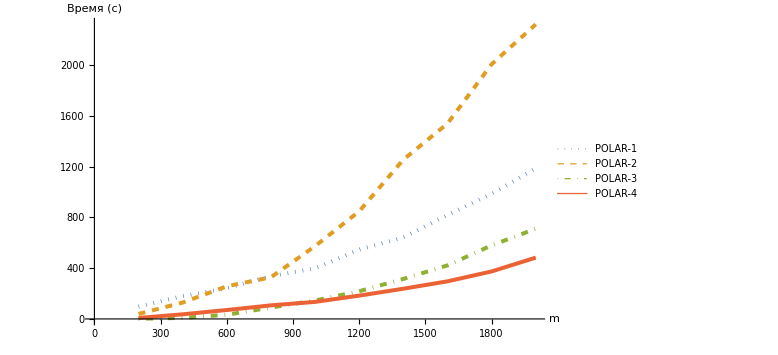

```mathematica
legend = FileBaseName/@Partition[TestResults,4][[1,{1,2,4,3},1,2]]
timedata = Map[SortBy[#,First]&, Join[
Map[StringReplace[#, __~~"-"~~(x:DigitCharacter..)~~".int":>{ToExpression[x]}][[1]]&, Partition[TestResults,4][[;;,{1,2,4,3},1,1]],{2}]//Transpose,
(Partition[TestResults,4][[;;,{1,2,4,3},2,1,2]]//Transpose) /.x_Real:>{x},3]]
timedata//TableForm
ListPlot[timedata,PlotLegends->{"POLAR-1", "POLAR-2", "POLAR-3", "POLAR-4   "}, Joined->True,InterpolationOrder->1,PlotStyle->{{Dotted,Thickness[0.005]}, {Dashed,Thickness[0.005]}, {DotDashed,Thickness[0.005]}, Thickness[0.005]}, AxesLabel->{"m","Время (с)" }, ImageSize->Large]
```